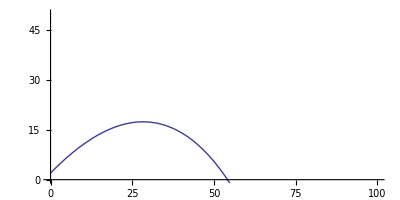

```mathematica
g=9.8; (*grav. constant*)
vt = 35;
V = 30; (*Initial V*)
θ = 50 Pi/180 ;(*50 degrees*)
y0=2; 
x0 = 0;
vy0 = V Sin[θ];
vx0 = V Cos[θ];

ode1={x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 +y'[t]^2]),y[0]==y0,y'[0]==vx0,x[0]==x0,x'[0]==vx0};
sol=NDSolve[ode1,{x,y},{t,0,4}];
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol]},{t,0,4},PlotRange->{{0,100},{0,50}}]
```

```mathematica
Manipulate[
g=9.8;
Module[
{result = NDSolve[{{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 +y'[t]^2]),y[0]==y0,y'[0]==V Sin[θ],x[0]==x0,x'[0]==V Cos[θ]}},{x,y},{t,0,time}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.result]},{t,0,time},PlotStyle->Blue,AxesLabel->{"x (m)","y (m)"},PlotRange->All,ImageSize->{500,300}]],
{{θ,50 Pi/180,"initial angle (rad)"},0,Pi/2,Appearance->"Labeled"},{{y0,2.,"initial height"},0.,2.,Appearance->"Labeled"},{{V,30.,"initial velocity"},0.,439.,Appearance->"Labeled"},
{{vt,35.,"terminal velocity"},0.,135.,Appearance->"Labeled"},{{time,5.,"time"},0.,100.,Appearance->"Labeled"}]
```

```mathematica
ExportString[{{"Projectile","Initial Angle","Initial Speed (m/s)"},{"Human Cannonball",π/4,31.2 },{"Golfball",π/4,33.3},{"Baseball",π/4,33.3}},"Table",Alignment->Center]
```

Projectile   	Initial Angle	Initial Speed (m/s)\r
Human Cannonball	    Pi/4     	       31.2        \r
    Golfball    	    Pi/4     	       33.3        \r
    Baseball    	    Pi/4     	       33.3

```mathematica
ExportString[{{"Cannonball Launches"},{"Initial Angle","Range"},{"5 deg","1700 m"},{"10 deg","2380 m"},{"15 deg","2750 m"}},"Table",Alignment->Center]
```

Cannonball Launches\r
   Initial Angle   	Range \r
       5 deg       	1700 m\r
      10 deg       	2380 m\r
      15 deg       	2750 m

```mathematica
ExportString[{{"Cannonball Launches In Ranch"},{"Initial Angle","Initial Velocity"},{"5 deg","288 m/s"},{"10 deg","206 m/s"},{"15 deg","171 m/s"}},"Table",Alignment->Center]
```

Cannonball Launches In Ranch\r
       Initial Angle        	Initial Velocity\r
           5 deg            	    288 m/s     \r
           10 deg           	    206 m/s     \r
           15 deg           	    171 m/s